17 Gráficos estadísticos
17.1 Tablas de frecuencias discretas

Vector de longitud 100 con números enteros aleatorios entre el 1 y el 6:

```mathematica
a=RandomInteger[{1,6},100]
```

{3,3,2,2,6,3,6,4,5,5,2,2,3,3,1,6,2,6,2,1,1,4,3,5,4,5,3,4,4,4,6,1,1,5,4,1,3,6,2,1,4,6,6,6,6,3,4,4,6,3,2,3,6,5,6,4,2,2,6,2,6,4,4,4,1,2,5,1,1,6,5,5,1,6,5,5,6,2,6,4,6,5,1,2,2,3,6,5,5,1,5,3,3,6,3,4,3,3,5,3}

Tabla de frecuencias:

```mathematica
Tally[a]//MatrixForm
```

(3 | 18
2 | 15
6 | 22
4 | 16
5 | 16
1 | 13)

Tabla de frecuencias ordenada:

```mathematica
Sort[Tally[a]]//MatrixForm
```

(1 | 13
2 | 15
3 | 18
4 | 16
5 | 16
6 | 22)

Diagrama de barras:

```mathematica
Sort[Tally[a]][[All,2]]
```

{13,15,18,16,16,22}

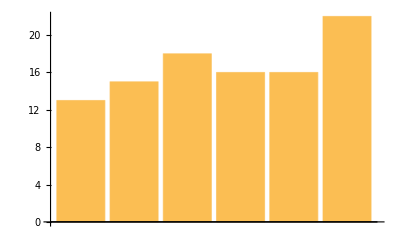

```mathematica
BarChart[Sort[Tally[a]][[All,2]]]
```

```mathematica
BarChart3D[Sort[Tally[a]][[All,2]]]
```

-Graphics3D-

Diagrama de sectores:

```mathematica
PieChart[Sort[Tally[a]][[All,2]]]
```

-Graphics-

```mathematica
PieChart3D[Sort[Tally[a]][[All,2]]]
```

-Graphics3D-

17.2 Recuento de clases e histogramas

Vector con 100 datos de números reales aleatorios entre el 1 y el 6:

```mathematica
a=RandomReal[{0,6},100]
```

{1.89489,0.172901,1.25687,1.01104,3.38001,2.33854,2.83404,1.5191,1.67156,2.52328,4.31904,5.77285,0.104656,4.34922,5.79045,5.59132,1.56036,0.101502,4.67523,1.01125,2.25692,1.38063,1.15224,2.18854,1.76062,4.70322,1.84691,4.06198,4.77482,0.881199,4.72956,1.96734,5.99834,0.611703,1.48498,1.46717,0.31927,3.91668,1.51876,0.0527118,4.38284,4.59177,1.95661,2.91996,3.25059,3.7929,1.26753,1.48192,3.02685,0.598411,3.61803,2.79565,5.3057,3.73877,2.18908,4.99146,3.24684,0.609395,0.873323,1.24634,2.94633,3.28621,2.90042,5.6189,0.950012,5.15255,5.03558,0.0913251,1.11905,3.98815,2.91939,1.33062,3.32618,2.28741,4.05387,2.58147,0.702024,2.01447,1.65762,0.337152,0.530127,1.38577,1.04331,2.66977,3.21001,4.77004,0.0354527,4.52615,0.380553,3.5895,5.47724,0.711932,2.21427,1.75154,3.73602,4.95736,1.36314,5.4537,1.66619,5.26652}

Recuento con clases de ancho 1:

```mathematica
BinCounts[a,{0,6,1}]
```

{18,27,16,14,14,11}

Recuento con clases de ancho 1.5:

```mathematica
BinCounts[a,{0,6,1.5}]
```

{33,28,19,20}

Recuento con clases de ancho 2:

```mathematica
BinCounts[a,{0,6,2}]
```

{45,30,25}

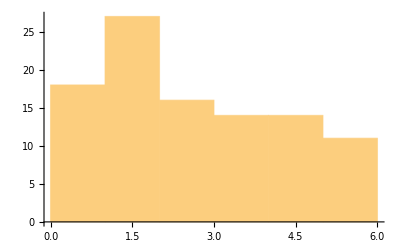

```mathematica
Histogram[a]
```

Vector con 1000 números generados de acuerdo a una distribución normal:

```mathematica
a=RandomVariate[NormalDistribution[0,1],1000];
```

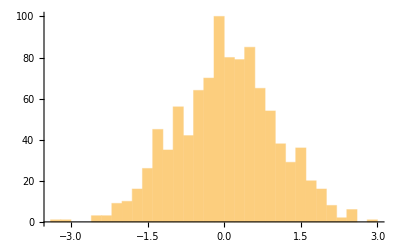

```mathematica
Histogram[a]
```

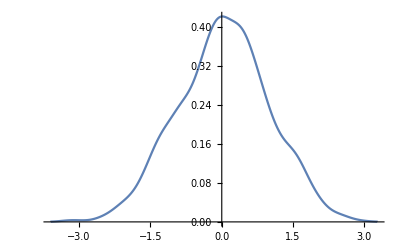

```mathematica
SmoothHistogram[a]
```

17.3 Diagrama de cajas y bigotes

```mathematica
a=RandomInteger[{1,6},100];
b=RandomInteger[{1,10},500];
```

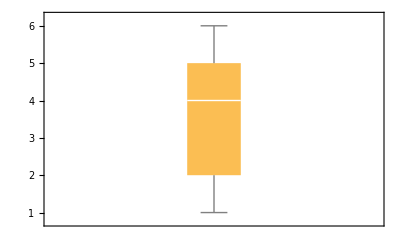

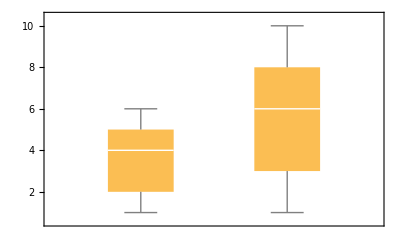

```mathematica
BoxWhiskerChart[a]
BoxWhiskerChart[{a,b}]
```

17.4 Diagrama de dispersión:

Representar los puntos (2,4), (3,1) y (2,2):

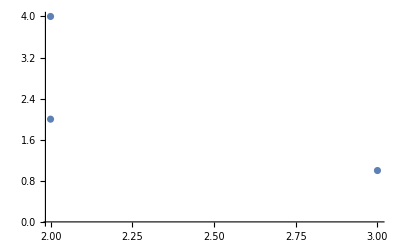

```mathematica
ListPlot[{{2,4},{3,1},{2,2}}]
```

Generar un conjunto de 100 puntos reales aleatorios en el intervalo [0,1] y representarlos en un diagrama de dispersión:

```mathematica
a=RandomReal[{0,1},{100,2}];
a//MatrixForm
```

(0.227202 | 0.26678
0.185655 | 0.718769
0.682608 | 0.140215
0.339417 | 0.304856
0.5239 | 0.702444
0.249672 | 0.828987
0.714222 | 0.0245565
0.0187925 | 0.53857
0.019154 | 0.489224
0.546349 | 0.327269
0.0767747 | 0.507036
0.279541 | 0.645772
0.653989 | 0.00118452
0.658753 | 0.202163
0.749195 | 0.0418078
0.894886 | 0.636618
0.663311 | 0.266096
0.412178 | 0.337924
0.321839 | 0.54109
0.0472103 | 0.103583
0.569772 | 0.1659
0.64872 | 0.0509007
0.278024 | 0.627486
0.971459 | 0.379731
0.38085 | 0.488195
0.53221 | 0.251158
0.9601 | 0.431162
0.206702 | 0.207003
0.285572 | 0.537157
0.874393 | 0.664011
0.464906 | 0.381137
0.882774 | 0.197113
0.838637 | 0.72941
0.763321 | 0.562356
0.350547 | 0.574419
0.122627 | 0.838487
0.88476 | 0.2114
0.169851 | 0.980089
0.533912 | 0.787584
0.329334 | 0.192105
0.651419 | 0.519261
0.602529 | 0.606606
0.846939 | 0.623128
0.687496 | 0.716231
0.576102 | 0.784101
0.648312 | 0.503873
0.140289 | 0.307292
0.585905 | 0.896819
0.0454473 | 0.316737
0.347587 | 0.576053
0.22375 | 0.575368
0.411609 | 0.202054
0.447686 | 0.472898
0.903322 | 0.775049
0.240853 | 0.249921
0.0779878 | 0.172182
0.772792 | 0.123958
0.723953 | 0.418141
0.493139 | 0.800868
0.322604 | 0.163427
0.109554 | 0.667736
0.146647 | 0.929289
0.673817 | 0.78144
0.225307 | 0.674447
0.353198 | 0.696562
0.898923 | 0.70993
0.589589 | 0.258337
0.790928 | 0.521409
0.139462 | 0.18765
0.544697 | 0.0899524
0.049499 | 0.250652
0.217939 | 0.648631
0.565872 | 0.976191
0.096996 | 0.500967
0.515903 | 0.799044
0.514941 | 0.751782
0.977319 | 0.138166
0.0614555 | 0.298962
0.99076 | 0.526578
0.412779 | 0.387339
0.655062 | 0.135337
0.765227 | 0.455339
0.0389412 | 0.380772
0.759723 | 0.234527
0.407543 | 0.290931
0.794106 | 0.130407
0.347143 | 0.768619
0.0115952 | 0.517346
0.403391 | 0.82533
0.740433 | 0.835666
0.793974 | 0.441146
0.814845 | 0.993545
0.813474 | 0.295168
0.0540198 | 0.0395657
0.820855 | 0.29358
0.0435712 | 0.84066
0.948476 | 0.759349
0.339899 | 0.50853
0.411287 | 0.0331069
0.0482205 | 0.281479)

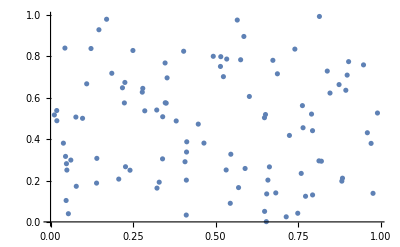

```mathematica
ListPlot[a]
```